```mathematica
(*plotting data from cpp program*)

4+Length[tomlist]/n-n
```

1000

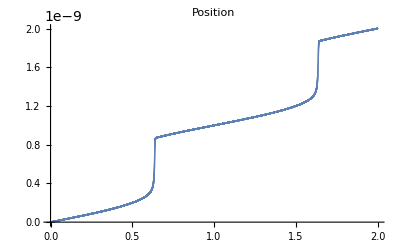

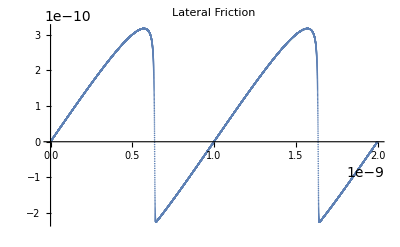

{0,4.53366×10^-17,1.85784×10^-16,4.6189×10^-16,9.06373×10^-16,1.54533×10^-15,2.39924×10^-15,3.48385×10^-15,4.81095×10^-15,6.38893×10^-15,8.2234×10^-15,1.03176×10^-14,1.26729×10^-14,49974,4.50455×10^-9,4.50457×10^-9,4.50458×10^-9,4.5046×10^-9,4.50461×10^-9,4.50463×10^-9,4.50464×10^-9,4.50466×10^-9,4.50467×10^-9,4.50469×10^-9,4.5047×10^-9,4.50472×10^-9,4.50473×10^-9}
 |  |  |  |

```mathematica
tomlist = ReadList["/home/storluffarn/phd-stuff/research/graphene/tomlin.txt",Number,RecordLists->False];
n=7;
h=1*^-13;

tompos = Table[tomlist[[1+n i]],{i,0,Length[tomlist]/n-n}];
tomvel = Table[tomlist[[2+n i]],{i,0,Length[tomlist]/n-n}];
tomacc= Table[tomlist[[3+n i]],{i,0,Length[tomlist]/n-n}];
tomkin = Table[tomlist[[4+n i]],{i,0,Length[tomlist]/n-n}];
tompot = Table[tomlist[[5+n i]],{i,0,Length[tomlist]/n-n}];
latfric = Table[tomlist[[6+n i]],{i,0,Length[tomlist]/n-n}];
time = Table[tomlist[[7+n i]],{i,0,Length[tomlist]/n-n}];
tomen = Table[tomlist[[4+n i]]+tomlist[[5+n i]],{i,1,Length[tomlist]/n-n}];

ListPlot[Thread@{time,tompos},PlotRange->All,PlotLabel->"Position"]
ListPlot[Thread@{time,tomvel},PlotRange->All,PlotLabel->"Velocity"];
ListPlot[Thread@{time,tomacc},PlotRange->All,PlotLabel->"Acceleration"];
ListPlot[{tomvel,tomacc/4*^13},PlotRange->All,PlotLabel->"Velocity and Acceleration (scaled)"];
ListPlot[tomkin,PlotRange->All,PlotLabel->"Kinetic Energy"];
ListPlot[tompot,PlotRange->All,PlotLabel->"Potential Energy"];
ListPlot[tomen,PlotRange->All,PlotLabel->"Total Energy"];
ListPlot[Thread@{time,latfric},PlotRange->All,PlotLabel->"Lateral Friction"]
```

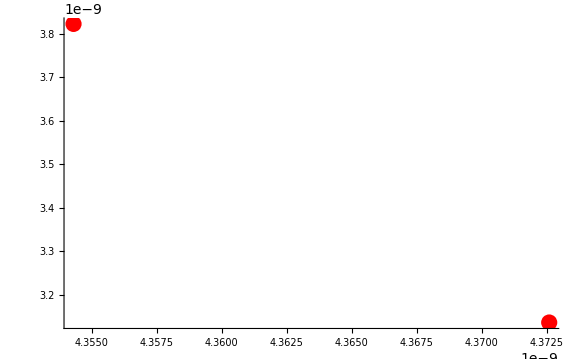

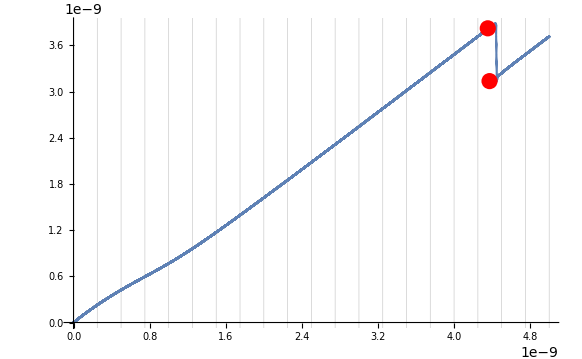

```mathematica
xlist=Import["~/phd-stuff/research/graphene/code/xout.csv"];
xlist=xlist[[All,1]];
xlist=Delete[xlist,1];
qlist=Import["~/phd-stuff/research/graphene/code/qout.csv"];
qlist=qlist[[All,1]];
qlist=Delete[qlist,1];
tomlist=Import["~/phd-stuff/research/graphene/code/tomout.csv"];
tomlist=tomlist[[All,3]];
tomlist=Delete[tomlist,1];
tlist=Import["~/phd-stuff/research/graphene/code/time.csv"];
tlist=tlist[[All,2]];
tlist=Delete[tlist,1];

plotlist =Thread@{tlist,tomlist};

gridlist=Table[i,{i,0,5*^-9,2.5*^-10}];
a=ListPlot[plotlist,GridLines->{gridlist, None}];
pts={{4.3543*^-09,3.82282*^-09},{4.3726*^-09,3.13683*^-09}};
b=ListPlot[pts,PlotStyle->{Red,PointSize[0.02]}]
(*b=Graphics[{PointSize[Large],Red,Point[{3.82282*^-09,4.3543*^-09}]}];
c=Graphics[{PointSize[Large],Red,Point[{3.13683*^-09,4.3726*^-09}]}];*)

Show[a,b]
```

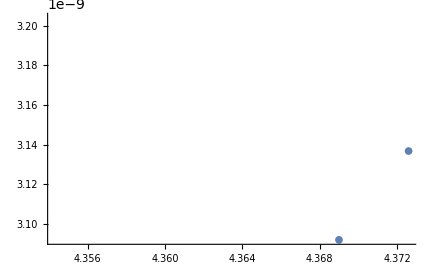

```mathematica
xlist=Import["~/phd-stuff/research/graphene/code/run3,0.csv"];
xlist=Delete[xlist,1];
plist=Table[{xlist[[i]][[1]],xlist[[i]][[2]]},{i,1,Length@xlist}];
ListPlot@plist
```

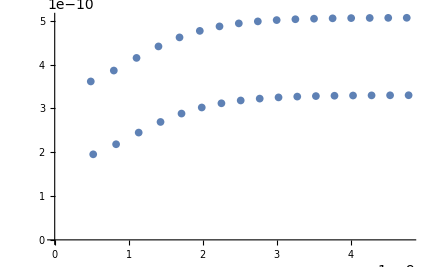

```mathematica
a=4.3543*^-09-4.3726*^-09
b=3.82282*^-09-3.13683*^-09 
b/a
```

-1.83×10^-11

6.8599×10^-10

-37.4858

b/a